# Úloha 2

Předpokládejme, že máme jednodinemzionální provázek s uhostí k = 1, umístěný v gravitačním poli g = -1. Také předpokládejme, že pod ním leží kámen, jehož horní hranice je popsána funkcí

```mathematica
g(x)=0.96 -0.25(-0.5+x)^2
```

Naším úkolem je nalézt výsledný tvar provázku.

## Bez podmínky

Nejprve se na začátek podívejme, jak bude vypadat řešení úlohy bez omezující podmínky (tj. než se postavil provázku kámen do cesty). Tuto úlohu vyřešíme pomocí soustavy n-1 lineármích rovnic pro n-1 nezmámých y_1, ..., y_(n-1) (jelikož počáteční a koncový bod jsou pevně dány, y_0 = y_n = 1). Tato soustava je dána tridiagonální maticí ve tvaru

```mathematica
({{2/h^2, -1/h^2, 0, 0, 0, 0}, {-1/h^2, 2/h^2, -1/h^2, 0, 0, 0}, {0, -1/h^2, 2/h^2, -1/h^2, 0, 0}, {0, 0, -1/h^2, 2/h^2, -1/h^2, 0}, {0, 0, 0, -1/h^2, 2/h^2, -1/h^2}, {0, 0, 0, 0, -1/h^2, 2/h^2}})
```

a vektorem pravé strany tvaru
(-1+1/h^2
-1
-1
-1
-1
-1+1/h^2)

```mathematica
n=200;h=(1/n);
A =(1/(h^(2)))*Total[{DiagonalMatrix[Array[-1&,n-2],-1],DiagonalMatrix[Array[2&,n-1]],DiagonalMatrix[Array[-1&,n-2],1]}] ;
b = ConstantArray[-1,n-1]+(1/(h^(2)))*UnitVector[n-1,1]+(1/(h^(2)))*UnitVector[n-1,n-1];
```

Nyní si určeme hodnotu n (počet bodů, ve kterých budeme počítat řešení), soustavu vyřešme a výsledné řešení vykresleme.

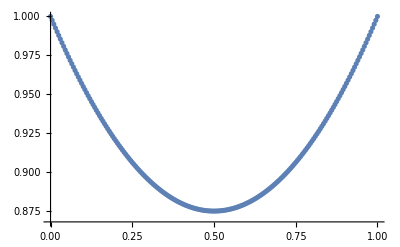

```mathematica
y=LinearSolve[A,b];
y=Insert[y,1,{{1},{n}}];
x=Table[i*h,{i,0,n}];
data = Transpose[{x,y}];

Show[ListPlot[data],ListLinePlot[data]]
```

## S podmínkou - řešení pomocí Newtonovy metody

Nyní se podívejme na řešení dané úlohy s podmínkou. To se skládá z vyřešení 2(n - 1) rovnic, nyní ale nelineárních, pro 2(n - 1) neznámých y_1, ... , y_(n-1), λ_1, ... , λ_(n-1) .

Nejprve si zadefinujme neznámé y_i, λ_i, funkci g(x), která nám určuje podmínku, a ekvidistantní dělení x.

```mathematica
n=100;h = 1/n;ro = 100;

y[i_] := Subscript[y,i];
l[i_] := Subscript[λ,i];
vars = Flatten[Table[{y[i], l[i]}, {i, 0, n }]];

g[x_]:=0.96−0.25(x−0.5)^2;(*(4/5) (Sqrt[Abs[x]]+Sqrt[1-x^2])-0.25,0.96−0.25(x−0.5)^2*)
x[i_] := i*h;
```

Pak soustava  je  tvaru je dána dvěma sadami nelineárních rovnic

```mathematica
eq1[i_]:=Piecewise[{{(-y[i-1] + 2*y[i] - y[i+1])/(h^2) + 1 + l[i] + ro*(y[i] - g[x[i]]), l[i] + ro(y[i]-g[x[i]]) <=0}, {(-y[i-1] + 2*y[i] - y[i+1])/(h^2) + 1 + l[i], l[i] + ro(y[i]-g[x[i]]) >0}}]

eq2[i_]:=Piecewise[{{y[i] - g[x[i]], l[i] + ro(y[i]-g[x[i]]) <=0}, {-l[i]/ro, l[i] + ro(y[i]-g[x[i]]) >0}}]

a = Flatten[Table[{eq1[i], eq2[i] }, {i, 1, n - 1}]]; 
a = Flatten[{a, y[0] - 1, y[n] - 1, l[0] , l[n]}];                 (* musíme přidat podmínky pro počáteční a koncový bod y_0 = y_n = 1 a λ_1 = λ_n = 0 *)
```

Nyní použijme Newtonovu metodu, kterou jsme si napsali v minulém úkolu, pro tuto soustavu.

```mathematica
JM = Grad[a,vars];
f[v_]:= a/.Table[vars[[i]]->v[[i]], {i,0,Length[vars]}];
J[v_]:= JM/.Table[vars[[i]]->v[[i]], {i,0,Length[vars]}];

v0=Table[1, {i,0,Length[vars] - 1}];    (* počáteční vektor je jedničkový vektor *)
J[v0];

iter[xn_]:=(A=N[J[xn]];
c=N[f[xn]];
delta = LinearSolve[A,-c];
xNew= delta+xn;
pocetit=pocetit+1;
xNew)                                                                     (* iterační schéma *)

pocetit=0;maxit=30;tol = 0.000001;     (* podmínky pro zastavení iteračního procesu jsou: velikost normy řešení je menší než nějaká určená tolerance nebo maximální počet iterací *)

(*res = NestWhile[iter,v0,Norm[f[#]]>tol&&pocetit<maxit&];*)
{t,res} =AbsoluteTiming[NestWhile[iter,v0,Norm[f[#]]>tol&&pocetit<maxit&]];
```

Vykresleme si získané řešení a pro zajímavost si vypišme, kolik iterací nás řešení stálo a jak dlouho trvalo.

22

10.6824

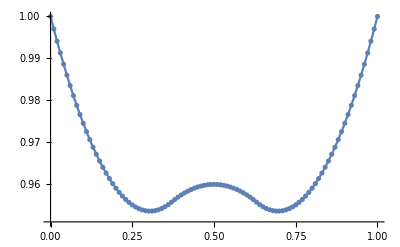

```mathematica
pocetit
t

ys = Table[res[[i*2+1]], {i, 0, n}];
xs = Table[x[i], {i, 0, n}];

Show[ListPlot[ Transpose[{xs,ys}]],ListLinePlot[ Transpose[{xs,ys}]]]
```

Nakonec si vykresleme, jak vypadá naše řešení společně s tvarem překážky pod provázkem (podmínkou g(x)).

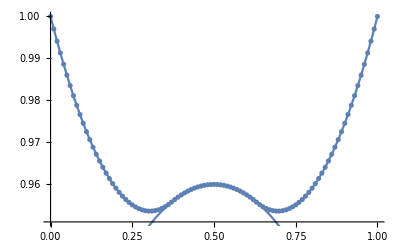

```mathematica
gs = Table[g[x[i]], {i, 0, n}];

Show[ListPlot[Transpose[{xs,ys}]],ListLinePlot[Transpose[{xs,ys}]], ListLinePlot[Transpose[{xs,gs}]]]
```

## S podmínkou - řešení pomocí funkce Solve

Nyní se podívejme, jaké řešení soustavy nelineárních rovnic nám dá samotná Mathematica a porovnejme to s výsledky, které jsme získali Newtonovou metodou.

```mathematica
n=15; h = 1/n; ro = 100;

x[i_] := i*h;
eq1[i_]:=Piecewise[{{(-y[i-1] + 2*y[i] - y[i+1])/(h^2) + 1 + l[i] + ro*(y[i] - g[x[i]]), l[i] + ro(y[i]-g[x[i]]) <=0}, {(-y[i-1] + 2*y[i] - y[i+1])/(h^2) + 1 + l[i], l[i] + ro(y[i]-g[x[i]]) >0}}]

eq2[i_]:=Piecewise[{{y[i] - g[x[i]], l[i] + ro(y[i]-g[x[i]]) <=0}, {-l[i]/ro, l[i] + ro(y[i]-g[x[i]]) >0}}]

eqs = Flatten[Table[{eq1[i] == 0, eq2[i] == 0}, {i, 1, n - 1}]];
eqs = Flatten[{eqs, y[0] == 1, y[n] == 1, l[0] == 0, l[n] == 0}];
vars = Flatten[Table[{y[i], l[i]}, {i, 0, n }]];
{t,sol} =AbsoluteTiming[Solve[eqs, vars]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
yn= Table[y[i], {i, 0, n}];
yn = yn /. Last[sol];
xn = Table[x[i], {i, 0, n}];
```

10.6824

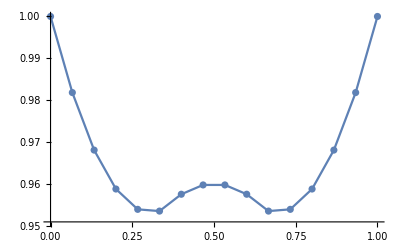

-Graphics-

```mathematica
t

Show[ListPlot[Transpose[{xn,yn}]],ListLinePlot[Transpose[{xn,yn}]]]
Show[ListPlot[ Transpose[{xs,ys}]],ListLinePlot[ Transpose[{xs,ys}]]]
```

## Jiný tvar kamene

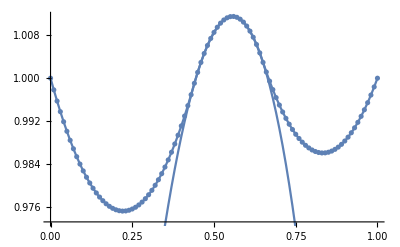

```mathematica
n=100;h = 1/n;ro = 100;
y[i_] := Subscript[y,i];
l[i_] := Subscript[λ,i];
vars = Flatten[Table[{y[i], l[i]}, {i, 0, n }]];

g[x_]:=(4/5) (Sqrt[Abs[x]]+Sqrt[1-x^2])-0.25

x[i_] := i*h;
eq1[i_]:=Piecewise[{{(-y[i-1] + 2*y[i] - y[i+1])/(h^2) + 1 + l[i] + ro*(y[i] - g[x[i]]), l[i] + ro(y[i]-g[x[i]]) <=0}, {(-y[i-1] + 2*y[i] - y[i+1])/(h^2) + 1 + l[i], l[i] + ro(y[i]-g[x[i]]) >0}}]

eq2[i_]:=Piecewise[{{y[i] - g[x[i]], l[i] + ro(y[i]-g[x[i]]) <=0}, {-l[i]/ro, l[i] + ro(y[i]-g[x[i]]) >0}}]

a = Flatten[Table[{eq1[i], eq2[i] }, {i, 1, n - 1}]]; 
a = Flatten[{a, y[0] - 1, y[n] - 1, l[0] , l[n]}];         
JM = Grad[a,vars];
f[v_]:= a/.Table[vars[[i]]->v[[i]], {i,0,Length[vars]}];
J[v_]:= JM/.Table[vars[[i]]->v[[i]], {i,0,Length[vars]}];

v0=Table[1, {i,0,Length[vars] - 1}];    
J[v0];

iter[xn_]:=(A=N[J[xn]];
c=N[f[xn]];
delta = LinearSolve[A,-c];
xNew= delta+xn;
pocetit=pocetit+1;
xNew)                                                                

pocetit=0;maxit=30;tol = 0.000001;  

res =NestWhile[iter,v0,Norm[f[#]]>tol&&pocetit<maxit&];

ys = Table[res[[i*2+1]], {i, 0, n}];
xs = Table[x[i], {i, 0, n}];
gs = Table[g[x[i]], {i, 0, n}];

Show[ListPlot[Transpose[{xs,ys}]],ListLinePlot[Transpose[{xs,ys}]], ListLinePlot[Transpose[{xs,gs}]]]
```